# Fang stuff

```mathematica
yE0=<|"2008"->(ρH/(4 10^-6))^0.606,"2010"->2(ρH/(6 10^-6))^0.7|>;
fQ0=<|"2008"->2qΔϵH,"2010"->qΔϵH|>;
P=<|"2008"->{{3.49979 10^(−1 ),−6.18200 10^(−2 ),−4.08124 10^(−2 ), 1.65414 10^(−2 )},
{5.85425 10^(−1 ),−5.00793 10^(−2 ), 5.69309 10^(−2 ),−4.02491 10^(−3 )},
{1.69692 10^(−1 ),−2.58981 10^(−2 ), 1.96822 10^(−2 ), 1.20505 10^(−3 )},
{-1.22271 10^(−1 ),−1.15532 10^(−2 ), 5.37951 10^(−6 ), 1.20189 10^(−3 )},
{1.57018 10^(0 ), 2.87896 10^(−1 ),−4.14857 10^(−1 ), 5.18158 10^(−2 )},
{8.83195 10^(−1 ), 4.31402 10^(−2 ),−8.33599 10^(−2 ), 1.02515 10^(−2 )},
{1.90953 10^(0 ),−4.74704 10^(−2 ),−1.80200 10^(−1 ), 2.46652 10^(−2 )},
{−1.29566 10^(0 ),−2.10952 10^(−1 ), 2.73106 10^(−1 ),−2.92752 10^(−2 )}}
,"2010"->{{1.24616 10^(0),1.45903 10^(0),−2.42269 10^(-1),5.95459 10^(-2)},
{2.23976 10^(0),−4.22918 10^(-7),1.36458 10^(-2),2.53332 10^(-3)},
{1.41754 10^(0),1.44597 10^(-1),1.70433 10^(-2),6.39717 10^(-4)},
{2.48775 10^(-1),−1.50890 10^(-1),6.30894 10^(-9),1.23707 10^(-3)},
{−4.65119 10^(-1),−1.05081 10^(-1),−8.95701 10^(-2),1.22450 10^(-2)},
{3.86019 10^(-1),1.75430 10^(-3),−7.42960 10^(-4),4.60881 10^(-4)},
{−6.45454 10^(-1),8.49555 10^(-4),−4.28581 10^(-2),−2.99302 10^(-3)},
{9.48930 10^(-1),1.97385 10^(-1),−2.50660 10^(-3),−2.06938 10^(-3)}}|>;
c[i_,E_,v_]:=Exp[Sum[P[[ToString[v]]][[i,j+1]](Log[E])^j,{j,0,3}]]
f[y_,E_,v_]:=c[1,E,v] y^c[2,E,v] Exp[-c[3,E,v] y^c[4,E,v]]+c[5,E,v] y^c[6,E,v] Exp[-c[7,E,v] y^c[8,E,v]]
```

## Unitless plots

```mathematica
(*Plot[{yE0["2008"],yE0["2010"]},{ρH,0,1},PlotLegends->{"y E_0 2008","y E_0 2010"},AxesLabel->{"ρ(z) H(z)",""}]
Plot[{fQ0["2008"],fQ0["2010"]},{qΔϵH,0,1},PlotLegends->{"f Q_0 2008","f Q_0 2010"},AxesLabel->{"q_tot(z) Δϵ H(z)",""}]*)
```

```mathematica
(*Manipulate[
LogLinearPlot[{
f[y,0.1,2008]
,f[y,1.0001,2008]
,f[y,10,2008]
,f[y,100,2008]
,f[y,1000,2008]
,f[y,0.1,2010]
,f[y,1.0001,2010]
,f[y,10,2010]
,f[y,100,2010]
,f[y,1000,2010]
},{y,0.1,10}
,PlotRange->{All,{0,1}}
,PlotLegends->Flatten[Table[ToString[e]<>" keV "<>ToString[v],{v,{2008,2010}},{e,{0.1,1,10,100,1000}}]]
,ImageSize->Large
,PlotStyle->{
{Black,Opacity[show0p1]}
,Darker@Green
,Brown
,Magenta
,{Red,Opacity[show1000]}
,{Black,Dashed,Opacity[show0p1]}
,{Darker@Green,Dashed}
,{Brown,Dashed}
,{Magenta,Dashed}
,{Red,Dashed,Opacity[show1000]}
},GridLines->Automatic]
,{show1000,{0,1}}
,{show0p1,{0,1}}
]*)
```

## MSIS Parameters

```mathematica
k=1.38064852 10^-16(*cm^2 g s^-2 K^-1*);
G=6.67408 10^-8(*cm^3 g^-1 s^-2*);
ME=5.9722 10^24 10^3(*g*);
RE=6.371 10^6 10^2(*cm*);
mu=1.660539040 10^-27 10^3(*g*);
Δϵ=35 10^-3(*keV*);
erg2kev=6.24150648 10^8;
Q0fang=1(*erg cm^-2 s^-1*);
msis=ToExpression[StringSplit/@StringSplit[StringReplace[Import["D:\\Files\\research\\thesis\\msis_maeve_null.lst"],"E"->"*10^"],"
"][[43;;]]];
z=msis[[;;,3]] 10^3 10^2(*cm*);
g=(G ME)/(RE+z)^2(*cm s^-2*);
n=msis[[;;,{4,5,6,9,10,11,12}]](*cm^-3*);
ρ=msis[[;;,7]](*g cm^-3*);
m=ρ/(Total/@n) (*g*);
T=msis[[;;,8]](*K*);
H=k T/(m g)(*cm*);
```

## 2008 vs 2010

```mathematica
(*y2008=yE0["2008"]/E0/.ρH->ρ H;
y2010=yE0["2010"]/Emono/.ρH->ρ H;
qtot2008=Q0/(2Δϵ)1/H f[y2008,E0,2008]/.{Q0->Q0fang erg2kev};
qtot2010=Qmono/(2Δϵ)1/H f[y2010,Emono,2010]/.{Qmono->Q0fang erg2kev};
plotA=ListLogLinearPlot[Flatten[Transpose[Table[{
Transpose[{qtot2008/.E0->10^exp,z 10^-5}]
,Transpose[{qtot2010/.Emono->10^exp,z 10^-5}]
},{exp,-1,3}]],1]
,PlotRange->{{10^1,10^5},{0,400}}
,AspectRatio->3/2
,Joined->True
,PlotStyle->Flatten[{Table[RGBColor[s,0,1-s],{s,0,1,1/4}],Table[{RGBColor[s,0,1-s],Dashed},{s,0,1,1/4}]},1]
,Frame->True
,FrameLabel->{"total ionization rate [cm^-3 s^-1]","altitude [km]"}
,PlotLabel->"F_10.7 = "<>ToString[msis[[1,-2]]] <>" A_p = "<>ToString[msis[[1,-1]]]<>" Q_0 = "<>ToString[Q0fang]<>" erg/cm^2/s"
,GridLines->All
,ImageSize->600
,LabelStyle->Directive[20,Black]
,PlotLegends->Flatten[{
Table["Fang 2008: E_0 = "<>ToString[e]<>" keV",{e,{0.1,1,10,100,1000}}]
,Table["Fang 2010: E_mono = "<>ToString[e]<>" keV",{e,{0.1,1,10,100,1000}}]
}]
]*)
```

## 2008 vs 2010 Maxwellian

General::munfl: Exp[-9.11255×10^12] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.10738×10^12] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.87405×10^12] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-204788.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-527088.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-176638.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

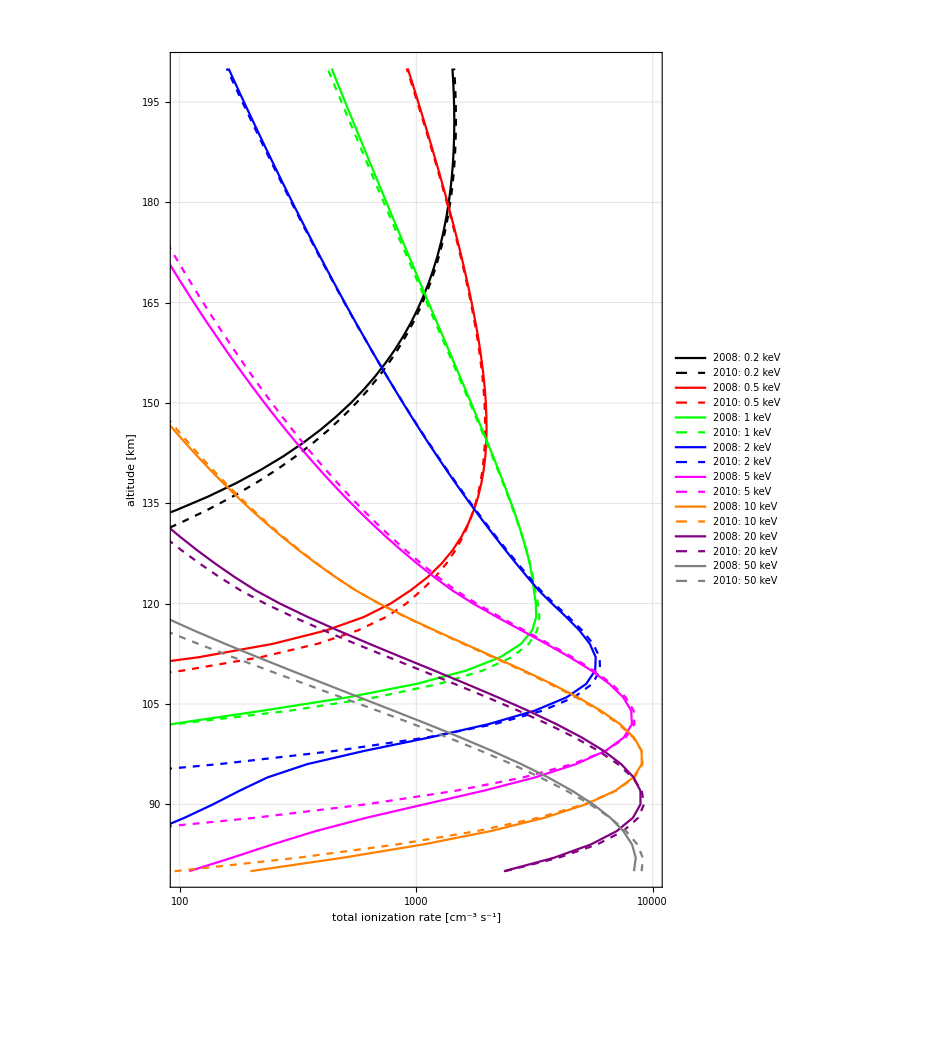

D:\Files\research\thesis\notebooks\FangMaxwellSpectrums_outsiderange.png

```mathematica
Q0keV=2erg2kev;(*keV*)
deps=35 10^-3;(*keV*)
lbins=64;
Ebin=10^Subdivide[-1,Log10[20E0keV],lbins];(*keV*)
dEbin=Ebin[[2;;]]-Ebin[[;;-2]];
Ebin=(Ebin[[2;;]]+Ebin[[;;-2]])/2;(*midpoint rule*)
phi=Q0keV/(2 E0keV^3)Ebin Exp[-Ebin/E0keV];
dQ0=Ebin phi dEbin;
ybin=2/Ebin(#/(6 10^-6))^0.7&/@(ρ H);
fbin=f[#,Ebin,2010]&/@ybin;
qtot2010=fbin.dQ0/deps/H;
y=1/E0keV((ρ H)/(4 10^-6))^0.606;
qtot2008=f[y,E0keV,2008] Q0keV/deps/H/2;
plot=ListLogLinearPlot[Flatten[
Table[{Transpose[{qtot2008/.E0keV->e,z 10^-5}],Transpose[{qtot2010/.E0keV->e,z 10^-5}]},{e,{0.2,0.5,1,2,5,10,20,50}}]
,1]
,PlotRange->{{10^2,10^4},{80,200}}
,AspectRatio->3/2
,Joined->True
(*,PlotMarkers->"OpenMarkers"*)
,PlotStyle->Flatten[{#,{#,Dashed}}&/@{Black,Red,Green,Blue,Magenta,Orange,Purple,Gray},1]
,PlotLegends->Flatten[Table[{"2008: "<>ToString[e]<>" keV","2010: "<>ToString[e]<>" keV"},{e,{0.2,0.5,1,2,5,10,20,50}}]]
,Frame->True
,FrameLabel->{"total ionization rate [cm^-3 s^-1]","altitude [km]"}
,GridLines->All
,ImageSize->700
,LabelStyle->Directive[20,Black]
]
Export[NotebookDirectory[]<>"FangMaxwellSpectrums_outsiderange.png",plot]
```

General::munfl: Exp[-204788.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-527088.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-176638.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

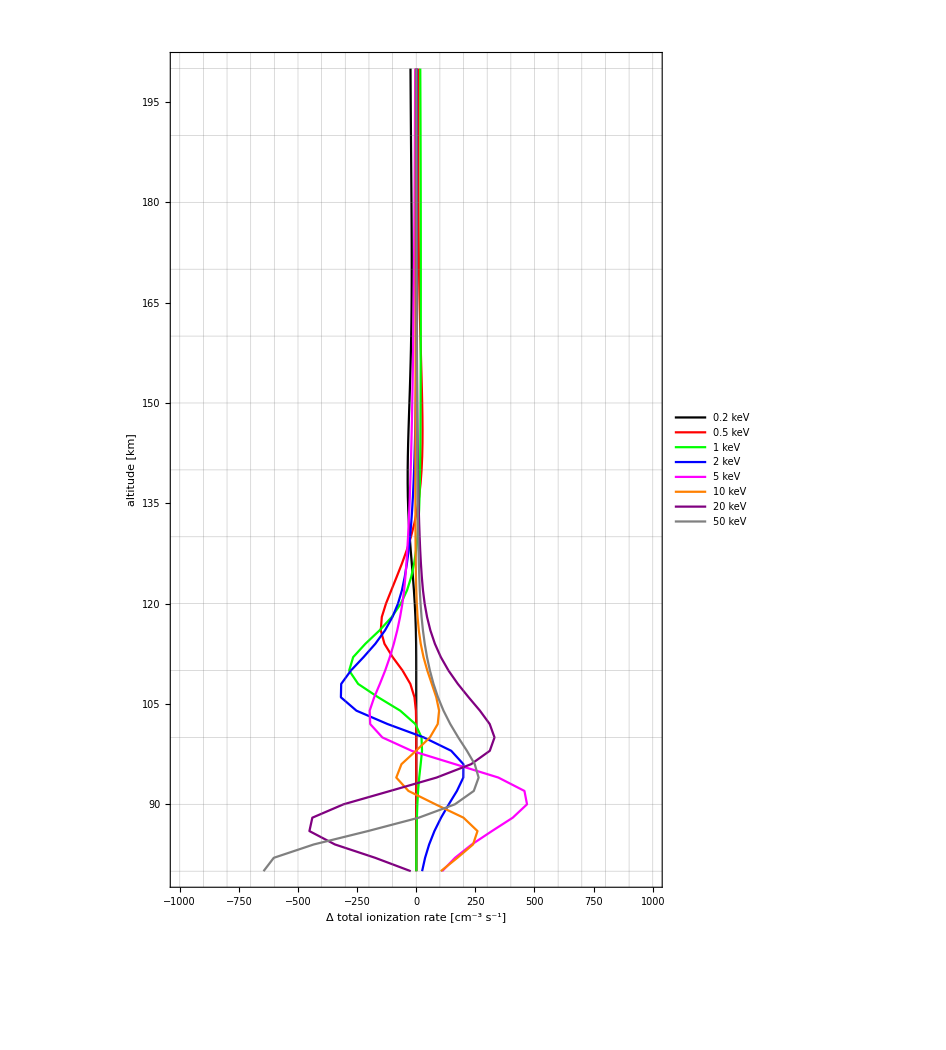

```mathematica
ListLinePlot[
Table[Transpose[{(qtot2008-qtot2010)/.E0keV->e,z 10^-5}],{e,{0.2,0.5,1,2,5,10,20,50}}]
,PlotRange->{{-1000,1000},{80,200}}
,AspectRatio->3/2
,Joined->True
(*,PlotMarkers->"OpenMarkers"*)
,PlotStyle->{Black,Red,Green,Blue,Magenta,Orange,Purple,Gray}
,PlotLegends->Flatten[Table[ToString[e]<>" keV",{e,{0.2,0.5,1,2,5,10,20,50}}]]
,Frame->True
,FrameLabel->{"Δ total ionization rate [cm^-3 s^-1]","altitude [km]"}
,GridLines->All
,ImageSize->700
,LabelStyle->Directive[20,Black]
]
```

General::munfl: Exp[-9.11255×10^12] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.10738×10^12] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.87405×10^12] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-204788.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-527088.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-176638.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

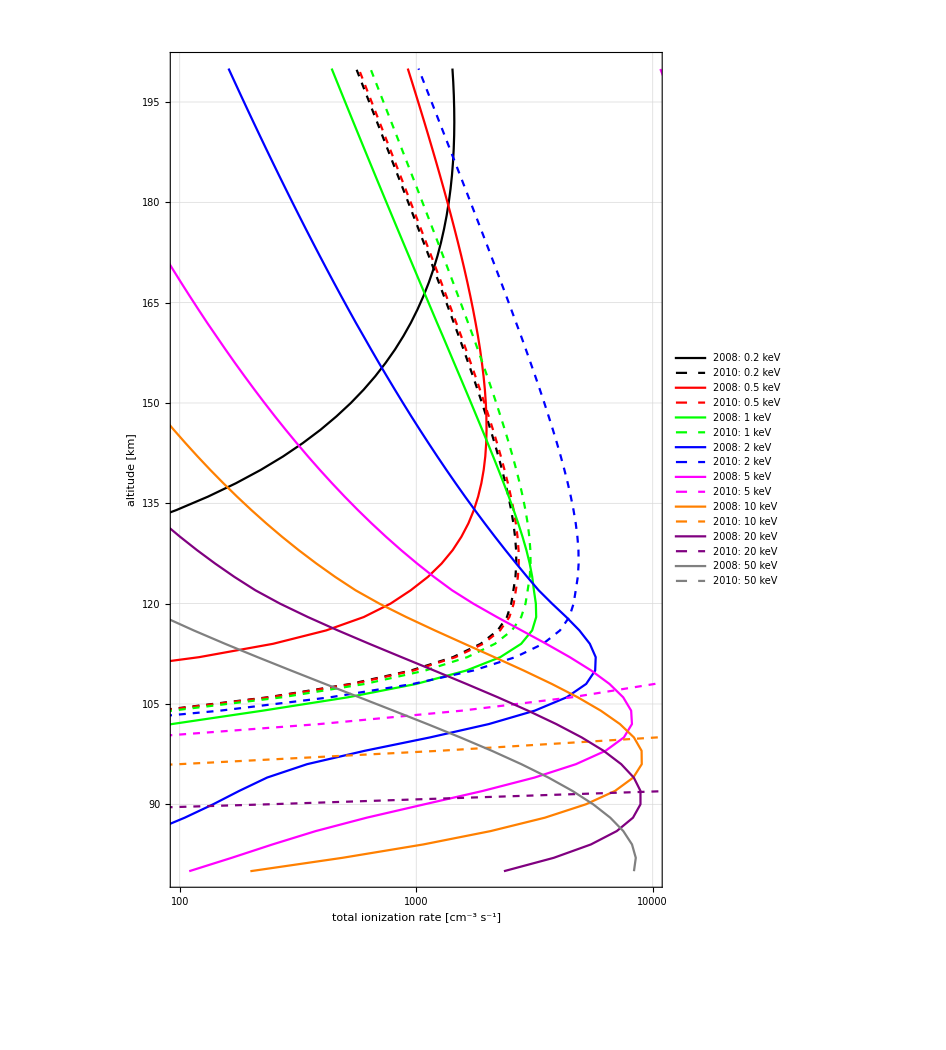

D:\Files\research\thesis\notebooks\FangMaxwellSpectrums_outsiderange.png

```mathematica
Q0keV=1erg2kev;(*keV*)
deps=35 10^-3;(*keV*)
lbins=63;
Ebin=10^Subdivide[-1,3,lbins];(*keV*)
dEbin=Ebin[[2;;]]-Ebin[[;;-2]];
Ebin=(Ebin[[2;;]]+Ebin[[;;-2]])/2;(*midpoint rule*)
phi=Q0keV/(0.8^2+(0.8+E0keV)^2)Ebin/0.8 Exp[-(Ebin-E0keV)/0.8];
dQ0=Ebin phi dEbin;
ybin=2/Ebin(#/(6 10^-6))^0.7&/@(ρ H);
fbin=f[#,Ebin,2010]&/@ybin;
qtot2010=fbin.dQ0/deps/H;
y=1/E0keV((ρ H)/(4 10^-6))^0.606;
qtot2008=f[y,E0keV,2008] Q0keV/deps/H/2;
plot=ListLogLinearPlot[Flatten[
Table[{Transpose[{qtot2008/.E0keV->e,z 10^-5}],Transpose[{qtot2010/.E0keV->e,z 10^-5}]},{e,{0.2,0.5,1,2,5,10,20,50}}]
,1]
,PlotRange->{{10^2,10^4},{80,200}}
,AspectRatio->3/2
,Joined->True
(*,PlotMarkers->"OpenMarkers"*)
,PlotStyle->Flatten[{#,{#,Dashed}}&/@{Black,Red,Green,Blue,Magenta,Orange,Purple,Gray},1]
,PlotLegends->Flatten[Table[{"2008: "<>ToString[e]<>" keV","2010: "<>ToString[e]<>" keV"},{e,{0.2,0.5,1,2,5,10,20,50}}]]
,Frame->True
,FrameLabel->{"total ionization rate [cm^-3 s^-1]","altitude [km]"}
,GridLines->All
,ImageSize->700
,LabelStyle->Directive[20,Black]
]
Export[NotebookDirectory[]<>"FangMaxwellSpectrums_outsiderange.png",plot]
```

## The above demonstrates the proper use of Fang 2010 is by doing the following: with E⧦E_mono and Q⧦Q_mono q_tot(z)=∫dq_tot(z)=∫(dQ(E))/(Δϵ H)f(y(z,E),E) dQ(E)=Eϕ_Mx(E,Q_0,E_0)dE y(z,E)=2/E((ρ(z)H(z))/(6 10^-6))^0.7 Doing this with ϕ_Mx(E,Q_0,E_0) being a Maxwellian from Fang 2008 gets you the same results.

## Gemini implementation

```mathematica
Q0keV=1erg2kev(*keV*);
deps=35 10^-3(*keV*);
lbins=64;
Ebin=10.^Subdivide[-1,3,lbins-1](*keV*);
dEbin=Ebin[[2;;]]-Ebin[[;;-2]]
Ebin=(Ebin[[2;;]]+Ebin[[;;-2]])/2(*midpoint rule*)
Dimensions/@{Ebin,dEbin}
```

{0.0157423,0.0182205,0.0210888,0.0244087,0.0282511,0.0326985,0.037846,0.0438039,0.0506996,0.0586809,0.0679186,0.0786105,0.0909856,0.105309,0.121887,0.141075,0.163283,0.188987,0.218738,0.253173,0.293028,0.339157,0.392548,0.454345,0.525869,0.608653,0.704468,0.815368,0.943725,1.09229,1.26424,1.46326,1.69361,1.96023,2.26881,2.62597,3.03936,3.51782,4.07161,4.71258,5.45444,6.3131,7.30692,8.4572,9.78856,11.3295,13.113,15.1773,17.5666,20.3319,23.5327,27.2372,31.525,36.4878,42.2318,48.88,56.5748,65.481,75.7892,87.7202,101.529,117.512,136.012}

{0.107871,0.124853,0.144507,0.167256,0.193586,0.224061,0.259333,0.300158,0.34741,0.4021,0.4654,0.538664,0.623462,0.721609,0.835207,0.966688,1.11887,1.295,1.49886,1.73482,2.00792,2.32401,2.68987,3.11331,3.60342,4.17068,4.82724,5.58716,6.46671,7.48471,8.66298,10.0267,11.6052,13.4321,15.5466,17.994,20.8267,24.1052,27.9,32.2921,37.3756,43.2593,50.0693,57.9514,67.0743,77.6333,89.8546,104.,120.372,139.321,161.253,186.638,216.019,250.026,289.385,334.941,387.669,448.697,519.332,601.087,695.711,805.232,931.994}

{{63},{63}}

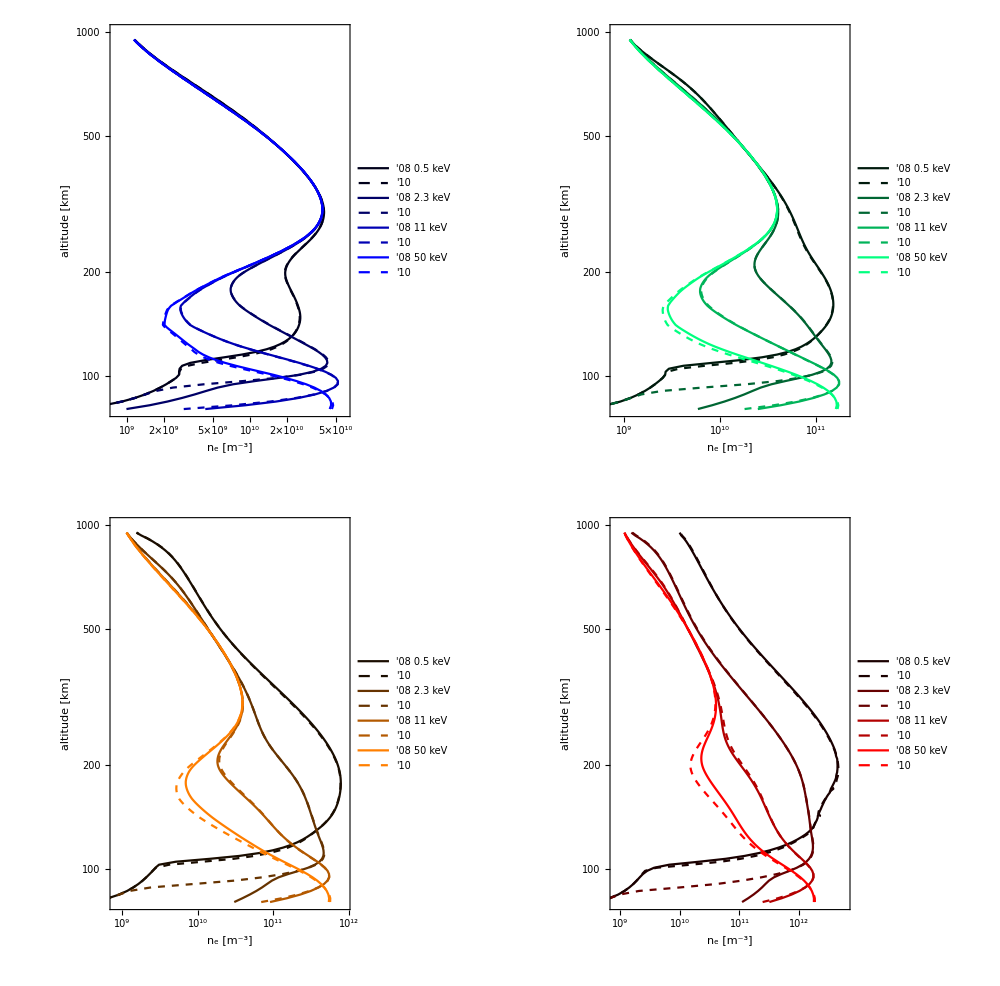

D:\Files\research\thesis\notebooks\gemini_maxwell_Fang08v10_comparison.png

```mathematica
alt=Import["D:\\Files\\research\\thesis\\runs\\preciptest_fang2010\\aurora_preciptest_base\\inputs\\simgrid.h5","/x1"][[3;;-3]]/1000;
ne2008=Table[Import["D:\\Files\\research\\thesis\\runs\\preciptest_fang2010\\pt_"<>e<>"_"<>q<>"_2008\\20150201_36000.000000.h5","/nsall"][[7,216/2,1,;;]],{e,{"5.00e+02","2.32e+03","1.08e+04","5.00e+04"}},{q,{"1.00e-01","1.00e+00","1.00e+01","1.00e+02"}}];
ne2010=Table[Import["D:\\Files\\research\\thesis\\runs\\preciptest_fang2010\\pt_"<>e<>"_"<>q<>"_2010\\20150201_36000.000000.h5","/nsall"][[7,216/2,1,;;]],{e,{"5.00e+02","2.32e+03","1.08e+04","5.00e+04"}},{q,{"1.00e-01","1.00e+00","1.00e+01","1.00e+02"}}];
plots=ListLogLogPlot[Flatten[Table[{
Transpose[{ne2008[[i,#1]],alt}]
,Transpose[{ne2010[[i,#1]],alt}]}
,{i,1,4,1}],1]
,PlotRange->{{8 10^8,#2},{80,1000}}
,Joined->True
,AspectRatio->1
,GridLines->All
,ImageSize->500
,Frame->True
,FrameLabel->{{"altitude [km]",""},{"n_e [m^-3]","Q_0 = "<>ToString[#4]<>" mW/m^2"}}
,FrameStyle->Directive[Black,15]
,LabelStyle->Directive[Black,15]
,PlotStyle->Flatten[Table[{#3,{#3,Dashed}},{c,0.1,1,0.3}],1]
,PlotLegends->Placed[Flatten[Table[{"'08 "<>ToString[v]<>" keV","'10"},{v,{0.5,2.3,11,50}}]],{Left,Center}]
]&@@@{
{1,6 10^10,RGBColor[0,0,c],0.1}
,{2,2 10^11,RGBColor[0,c,c/2],1}
,{3,9 10^11,RGBColor[c,c/2,0],10}
,{4,6 10^12,RGBColor[c,0,0],100}
};
plot=GraphicsGrid[Partition[plots,2],ImageSize->1000,Spacings->0]
Export[NotebookDirectory[]<>"gemini_maxwell_Fang08v10_comparison.png",plot]
```

```mathematica
test="1.08e+04_1.00e+01";
test="5.00e+02_1.00e+02";
(*test="5.00e+02_1.00e+01";*)
test2008=Import["D:\\Files\\research\\thesis\\runs\\preciptest_fang2010\\pt_"<>test<>"_2008\\20150201_36000.000000.h5","/nsall"][[7,;;,1]];
test2010=Import["D:\\Files\\research\\thesis\\runs\\preciptest_fang2010\\pt_"<>test<>"_2010\\20150201_36000.000000.h5","/nsall"][[7,;;,1]];
ListDensityPlot[test2008//Transpose,ImageSize->1000,AspectRatio->0.1]
ListDensityPlot[test2010//Transpose,ImageSize->1000,AspectRatio->0.1]
ListDensityPlot[100(test2010/test2008-1)//Transpose,ImageSize->1000,AspectRatio->0.1,PlotLegends->Automatic]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
te2010=Import["D:\\Files\\research\\thesis\\runs\\preciptest_fang2010\\pt_"<>test<>"_2010\\20150201_36000.000000.h5","/Tsall"][[7,;;,1]];
te2008=Import["D:\\Files\\research\\thesis\\runs\\preciptest_fang2010\\pt_"<>test<>"_2008\\20150201_36000.000000.h5","/Tsall"][[7,;;,1]];
ListDensityPlot[te2008//Transpose,ImageSize->1000,AspectRatio->0.1]
ListDensityPlot[te2010//Transpose,ImageSize->1000,AspectRatio->0.1,PlotLegends->Automatic]
```

-Graphics-

-Graphics-

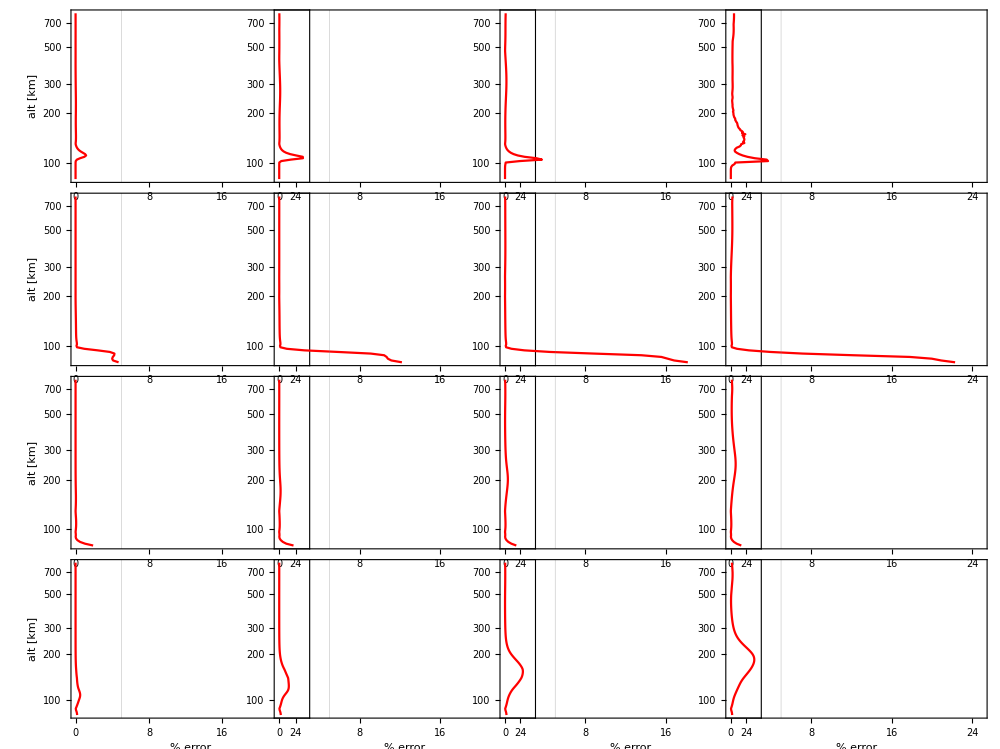

D:\Files\research\thesis\notebooks\gemini_maxwell_Fang08v10_error.png

```mathematica
test2008=Log10[Table[Import["D:\\Files\\research\\thesis\\runs\\preciptest_fang2010\\pt_"<>e<>"_"<>q<>"_2008\\20150201_36000.000000.h5","/nsall"][[7,;;,1,;;]],{e,{"5.00e+02","2.32e+03","1.08e+04","5.00e+04"}},{q,{"1.00e-01","1.00e+00","1.00e+01","1.00e+02"}}]];
test2010=Log10[Table[Import["D:\\Files\\research\\thesis\\runs\\preciptest_fang2010\\pt_"<>e<>"_"<>q<>"_2010\\20150201_36000.000000.h5","/nsall"][[7,;;,1,;;]],{e,{"5.00e+02","2.32e+03","1.08e+04","5.00e+04"}},{q,{"1.00e-01","1.00e+00","1.00e+01","1.00e+02"}}]];
names=Table["E0 = "<>e<>" eV
Q0 = "<>q<>" mW/m^2",{e,{"5.00e+02","2.32e+03","1.08e+04","5.00e+04"}},{q,{"1.00e-01","1.00e+00","1.00e+01","1.00e+02"}}];
error=Map[Max,Abs[Transpose[100(test2010/test2008-1),4<->3]],{3}];
plot=GraphicsGrid[Table[ListLogPlot[Transpose[{error[[i,j]],alt}]
,Joined->True
,FrameLabel->{{If[j==1,"alt [km]",""],""},{If[i==4,"% error",""],Style[names[[i,j]],Bold]}}
,LabelStyle->Directive[Black,13]
,FrameStyle->Directive[Black,13]
,GridLines->{{5},None}
,ImageSize->200
,PlotStyle->Red
,Frame->True
,PlotRange->{{0,25},{80,800}}
],{i,1,4},{j,1,4}],ImageSize->1000,Spacings->{-60,-10}]
Export[NotebookDirectory[]<>"gemini_maxwell_Fang08v10_error.png",plot]
```

## Kappa Distribution

```mathematica
phi=Q0/(2 E0^3)Gamma[κ+1]/(κ^(3/2)Gamma[κ-1/2])EE(1+EE/(κ E0))^(-κ-1);
phiM=Series[phi,{κ,∞,0}]//Normal
FullSimplify[Integrate[phi,{EE,0,∞},Assumptions->{κ>2,E0>0}],Assumptions->κ>2]
FullSimplify[Integrate[EE phi,{EE,0,∞},Assumptions->{κ>2,E0>0}]/Integrate[phi,{EE,0,∞},Assumptions->{κ>2,E0>0}],Assumptions->κ>2]
Integrate[EE phiM,{EE,0,∞},Assumptions->{κ>2,E0>0}]/Integrate[phiM,{EE,0,∞},Assumptions->{κ>2,E0>0}]
```

(ⅇ^(-EE/E0) EE Q0)/(2 E0^3)

(Q0 √κ Gamma[-1+κ])/(2 E0 Gamma[-1/2+κ])

(2 E0 κ)/(-2+κ)

2 E0

```mathematica
Manipulate[
LogLogPlot[{
phi/.{Q0->1 erg2kev,E0->EE0,κ->5}
,phiM/.{Q0->1 erg2kev,E0->EE0,κ->5}
},{EE,0.1,1000},Frame->True,GridLines->{{EE0},All},ImageSize->Large,PlotLegends->{"gemini","maxwellian"},PlotRange->{{0.1,1000},{10,10^9}}]
,{{EE0,1},0.1,100}]
```

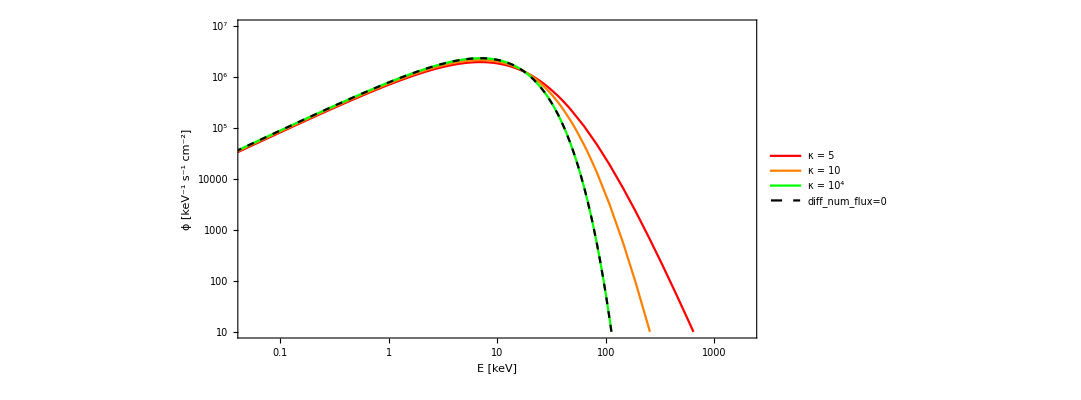

D:\Files\research\thesis\notebooks\fang2010_kappa-test_spectra.png

```mathematica
erg2kev=6.24150648 10^8;
plot=LogLogPlot[{
phi/.{κ->5,E0->7,Q0->1 erg2kev}
,phi/.{κ->10,E0->7,Q0->1 erg2kev}
,phi/.{κ->10^4,E0->7,Q0->1 erg2kev}
,phiM/.{E0->7,Q0->1erg2kev}
},{EE,0.01,10000}
,PlotRange->{{0.05,2000},{10^1,10^7}}
,GridLines->{{0.1,7,1000},All}
,AspectRatio->1/2
,ImageSize->800
,PlotStyle->{Red,Orange,Green,{Black,Dashed}}
,Frame->True
,PlotLegends->Placed[{"κ = 5","κ = 10","κ = 10^4","diff_num_flux=0"},{Right,Top}]
,FrameStyle->Directive[Black,20]
,LabelStyle->Directive[Black,18]
,FrameLabel->{"E [keV]","ϕ [keV^-1 s^-1 cm^-2]"}
]
Export[NotebookDirectory[]<>"fang2010_kappa-test_spectra.png",plot]
```

```mathematica
alt=Import["D:\\Files\\research\\thesis\\runs\\kappatest\\kappadefault\\inputs\\simgrid.h5","/x1"][[3;;-3]]/1000;
ne5=Import["D:\\Files\\research\\thesis\\runs\\kappatest\\kappa5\\20150201_36000.000000.h5","/nsall"][[7,216/2,1,;;]];
ne10=Import["D:\\Files\\research\\thesis\\runs\\kappatest\\kappa10\\20150201_36000.000000.h5","/nsall"][[7,216/2,1,;;]];
nedefault=Import["D:\\Files\\research\\thesis\\runs\\kappatest\\kappadefault\\20150201_36000.000000.h5","/nsall"][[7,216/2,1,;;]];
nemaxwell=Import["D:\\Files\\research\\thesis\\runs\\kappatest\\maxwellian\\20150201_36000.000000.h5","/nsall"][[7,216/2,1,;;]];
```

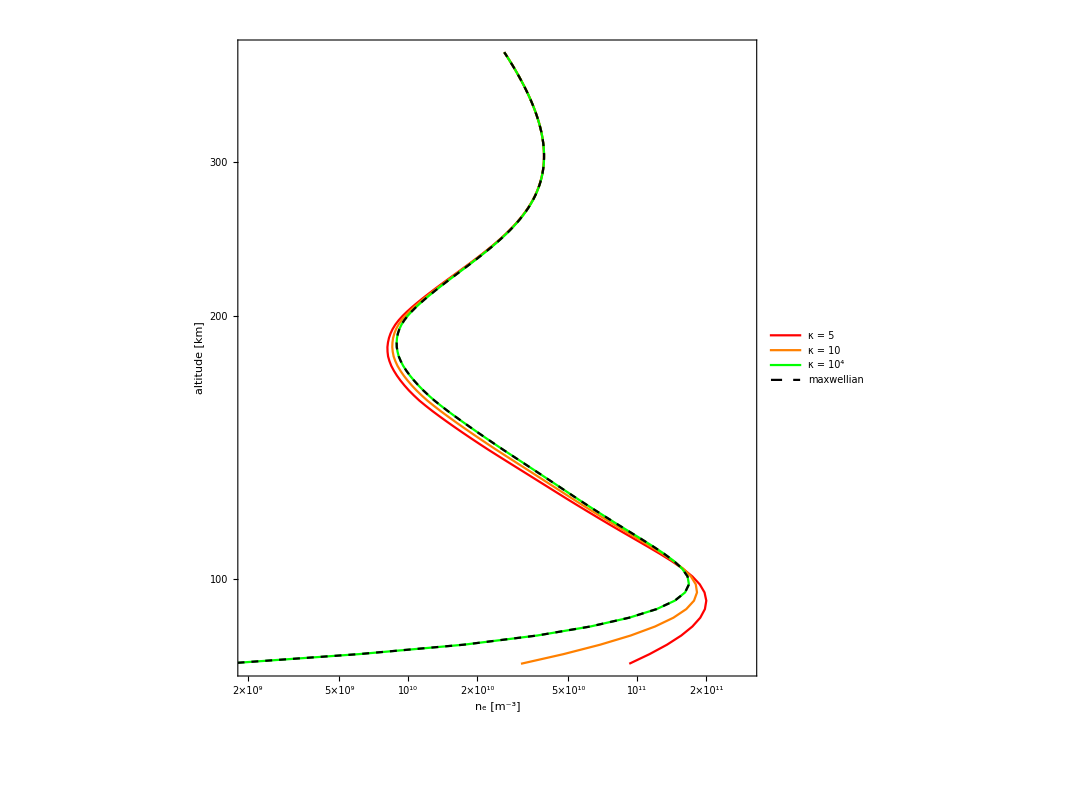

D:\Files\research\thesis\notebooks\fang2010_kappa-test.png

```mathematica
plot=ListLogLogPlot[{
Transpose[{ne5,alt}]
,Transpose[{ne10,alt}]
,Transpose[{nedefault,alt}]
,Transpose[{nemaxwell,alt}]
}
,Joined->True
,PlotRange->{{2 10^9,3 10^11},{80,400}}
,GridLines->All
,AspectRatio->1
,ImageSize->800
,PlotStyle->{Red,Orange,Green,{Black,Dashed}}
,Frame->True
,PlotLegends->Placed[{"κ = 5","κ = 10","κ = 10^4","maxwellian"},{Right,Top}]
,FrameStyle->Directive[Black,20]
,LabelStyle->Directive[Black,18]
,FrameLabel->{"n_e [m^-3]","altitude [km]"}
]
Export[NotebookDirectory[]<>"fang2010_kappa-test.png",plot]
```

## Bi-Maxwellian

```mathematica
phi=Q0/(2E0)1/2(EE/E0^2 Exp[-EE/E0]+EE/(ff E0)^2 Exp[-EE/(ff E0)]);
Integrate[phi,{EE,0,∞},Assumptions->{E0>0,Q0>0,ff>0}]
phiM=phi/.ff->1
```

Q0/(2 E0)

(ⅇ^(-EE/E0) EE Q0)/(2 E0^3)

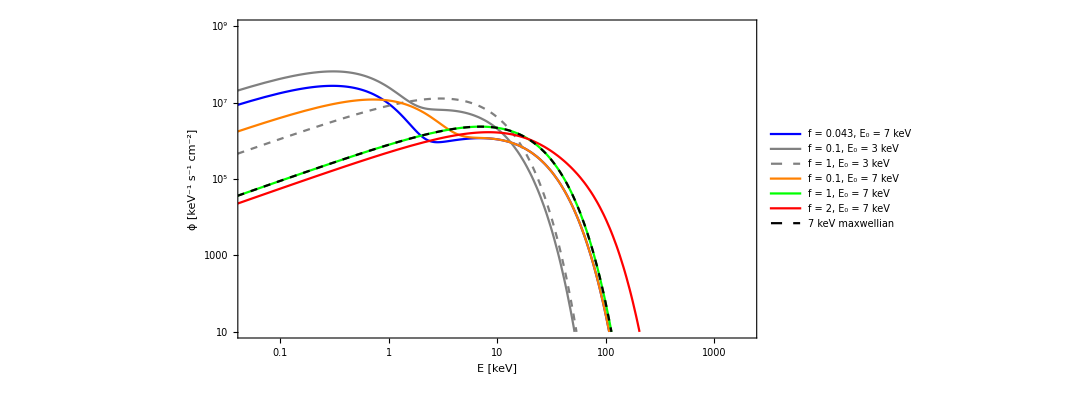

D:\Files\research\thesis\notebooks\fang2010_bimaxwellian-test_spectra.png

```mathematica
erg2kev=6.24150648 10^8;
plot=LogLogPlot[{
phi/.{ff->0.043,E0->7,Q0->1 erg2kev}
,phi/.{ff->0.1,E0->3,Q0->1 erg2kev}
,phi/.{ff->1,E0->3,Q0->1 erg2kev}
,phi/.{ff->0.1,E0->7,Q0->1 erg2kev}
,phi/.{ff->1,E0->7,Q0->1 erg2kev}
,phi/.{ff->2,E0->7,Q0->1 erg2kev}
,phiM/.{E0->7,Q0->1erg2kev}
},{EE,0.01,10000}
,PlotRange->{{0.05,2000},{10^1,10^9}}
,GridLines->{{0.3,0.7,3,7,14},All}
,AspectRatio->1/2
,ImageSize->800
,PlotStyle->{Blue,Gray,{Gray,Dashed},Orange,Green,Red,{Black,Dashed}}
,Frame->True
,PlotLegends->Placed[{"f = 0.043, E_0 = 7 keV","f = 0.1, E_0 = 3 keV","f = 1, E_0 = 3 keV","f = 0.1, E_0 = 7 keV","f = 1, E_0 = 7 keV","f = 2, E_0 = 7 keV","7 keV maxwellian"},{Right,Top}]
,FrameStyle->Directive[Black,20]
,LabelStyle->Directive[Black,18]
,FrameLabel->{"E [keV]","ϕ [keV^-1 s^-1 cm^-2]"}
]
Export[NotebookDirectory[]<>"fang2010_bimaxwellian-test_spectra.png",plot]
```

```mathematica
Clear[phi]
phi[E_,f_,Q0_,E0_]:=Total[Q0/(2E0)1/Length[f](E/(f E0)^2 Exp[-E/(f E0)])]
phi[EE,{1,1,1,1,1},Q,E0]
Integrate[phi[EE,{f1,f2,f3,f4,f5},Q0,E0],{EE,0,∞},Assumptions->{E0>0,Q0>0,f1>0,f2>0,f3>0,f4>0,f5>0}]
```

(ⅇ^(-EE/E0) EE Q)/(2 E0^3)

Q0/(2 E0)

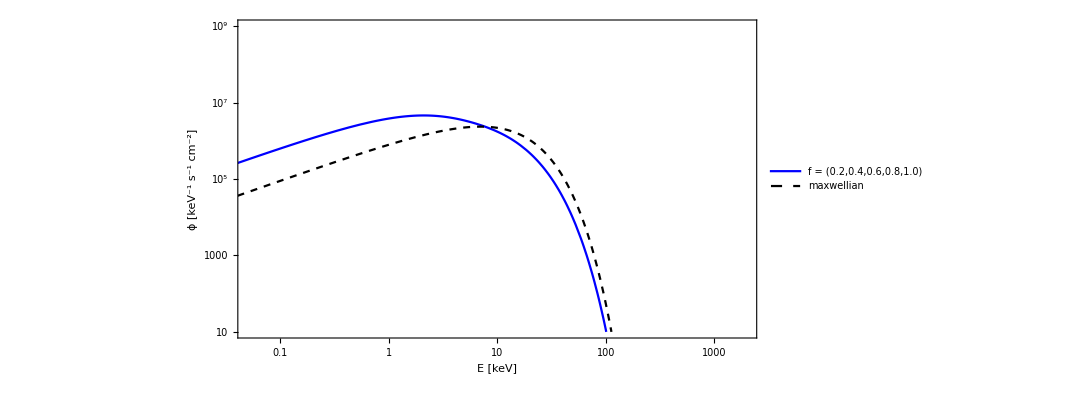

D:\Files\research\thesis\notebooks\fang2010_bimaxwellian-test_multiple.png

```mathematica
erg2kev=6.24150648 10^8;
plot=LogLogPlot[{
phi[EE,{0.2,0.4,0.6,0.8,1.0},1 erg2kev,7]
,phiM/.{E0->7,Q0->1erg2kev}
},{EE,0.01,1000}
,PlotRange->{{0.05,2000},{10^1,10^9}}
,GridLines->{{0.3,0.7,3,7,14},All}
,AspectRatio->1/2
,ImageSize->800
,PlotStyle->{Blue,{Black,Dashed}}
,Frame->True
,PlotLegends->Placed[{"f = (0.2,0.4,0.6,0.8,1.0)","maxwellian"},{Right,Top}]
,FrameStyle->Directive[Black,20]
,LabelStyle->Directive[Black,18]
,FrameLabel->{"E [keV]","ϕ [keV^-1 s^-1 cm^-2]"}
]
Export[NotebookDirectory[]<>"fang2010_bimaxwellian-test_multiple.png",plot]
```

```mathematica
alt=Import["D:\\Files\\research\\thesis\\runs\\bimaxtest\\0p1\\inputs\\simgrid.h5","/x1"][[3;;-3]]/1000;
ne0p043=Import["D:\\Files\\research\\thesis\\runs\\bimaxtest\\0p043\\20150201_36000.000000.h5","/nsall"][[7,216/2,1,;;]];
ne0p13keV=Import["D:\\Files\\research\\thesis\\runs\\bimaxtest\\0p1_3keV\\20150201_36000.000000.h5","/nsall"][[7,216/2,1,;;]];
ne13keV=Import["D:\\Files\\research\\thesis\\runs\\bimaxtest\\1_3keV\\20150201_36000.000000.h5","/nsall"][[7,216/2,1,;;]];
ne0p1=Import["D:\\Files\\research\\thesis\\runs\\bimaxtest\\0p1\\20150201_36000.000000.h5","/nsall"][[7,216/2,1,;;]];
ne1=Import["D:\\Files\\research\\thesis\\runs\\bimaxtest\\1\\20150201_36000.000000.h5","/nsall"][[7,216/2,1,;;]];
ne2=Import["D:\\Files\\research\\thesis\\runs\\bimaxtest\\2\\20150201_36000.000000.h5","/nsall"][[7,216/2,1,;;]];
nemaxwell=Import["D:\\Files\\research\\thesis\\runs\\bimaxtest\\maxwellian\\20150201_36000.000000.h5","/nsall"][[7,216/2,1,;;]];
nenull=Import["D:\\Files\\research\\thesis\\runs\\bimaxtest\\null\\20150201_36000.000000.h5","/nsall"][[7,216/2,1,;;]];
```

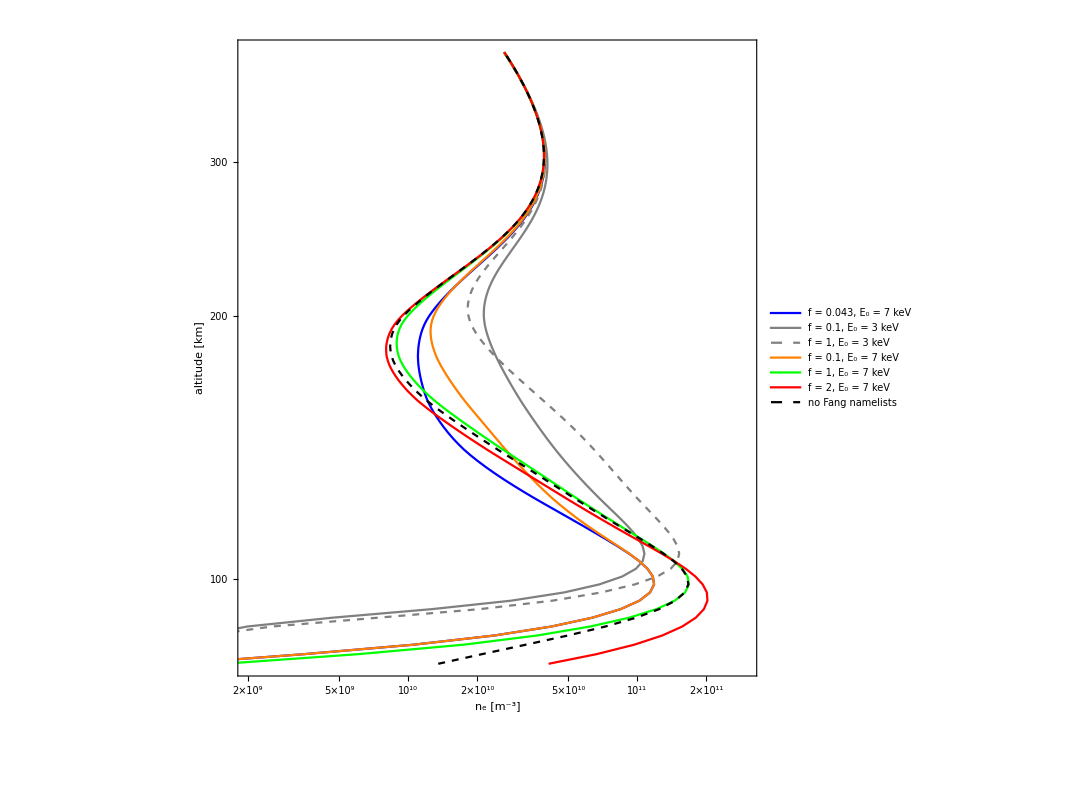

D:\Files\research\thesis\notebooks\fang2010_bimaxwellian-test.png

```mathematica
plot=ListLogLogPlot[{
Transpose[{ne0p043,alt}]
,Transpose[{ne0p13keV,alt}]
,Transpose[{ne13keV,alt}]
,Transpose[{ne0p1,alt}]
,Transpose[{ne1,alt}]
,Transpose[{ne2,alt}]
,Transpose[{nenull,alt}]
}
,Joined->True
,PlotRange->{{2 10^9,3 10^11},{80,400}}
,GridLines->All
,AspectRatio->1
,ImageSize->800
,PlotStyle->{Blue,Gray,{Gray,Dashed},Orange,Green,Red,{Black,Dashed}}
,Frame->True
,PlotLegends->Placed[{"f = 0.043, E_0 = 7 keV","f = 0.1, E_0 = 3 keV","f = 1, E_0 = 3 keV","f = 0.1, E_0 = 7 keV","f = 1, E_0 = 7 keV","f = 2, E_0 = 7 keV","no Fang namelists"},{Right,Top}]
,FrameStyle->Directive[Black,20]
,LabelStyle->Directive[Black,18]
,FrameLabel->{"n_e [m^-3]","altitude [km]"}
]
Export[NotebookDirectory[]<>"fang2010_bimaxwellian-test.png",plot]
```

## Accelerated Distribution

```mathematica
phi=Q0/(2 E0^2)Piecewise[{{(EE-V0)/E0 Exp[(V0-EE)/E0],EE>V0}},0];
phiM=Q0/(2 E0^3)EE Exp[-EE/E0];
Integrate[EE phi,{EE,0,∞},Assumptions->{Q0>0,E0>0,V0>0}]/Integrate[phi,{EE,0,∞},Assumptions->{Q0>0,E0>0,V0>0}]
Integrate[phi,{EE,0,∞},Assumptions->{Q0M>0,E0>0,V0>0}]
Integrate[phiM,{EE,0,∞},Assumptions->{Q0M>0,E0>0}]
```

2 E0+V0

Q0/(2 E0)

Q0/(2 E0)

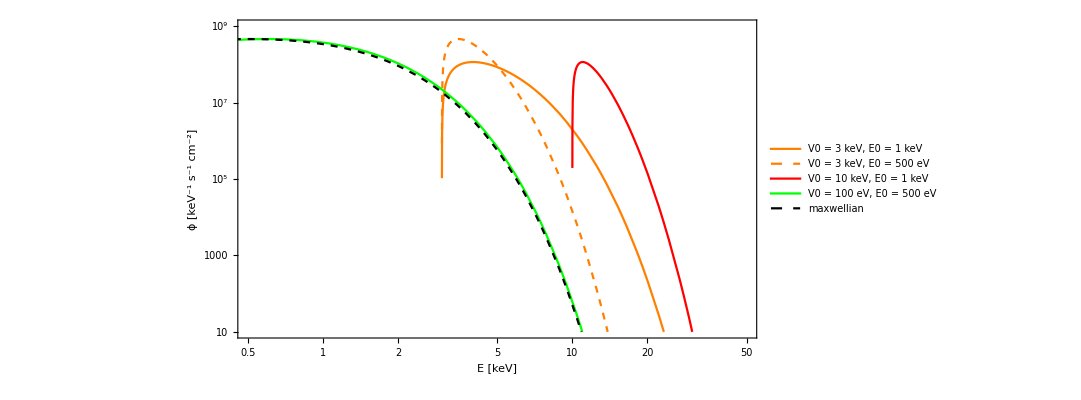

D:\Files\research\thesis\notebooks\fang2010_invertedV-test_spectra.png

```mathematica
erg2kev=6.24150648 10^8;
plot=LogLogPlot[{
phi/.{E0->1,Q0->1 erg2kev,V0->3}
,phi/.{E0->0.5,Q0->1 erg2kev,V0->3}
,phi/.{E0->1,Q0->1 erg2kev,V0->10}
,phi/.{E0->0.5,Q0->1 erg2kev,V0->0.1}
,phiM/.{E0->0.5,Q0->1 erg2kev}
},{EE,0.01,100}
,PlotRange->{{0.5,50},{10^1,10^9}}
,GridLines->{{1,3,8},All}
,AspectRatio->1/2
,ImageSize->800
,PlotStyle->{Orange,{Orange,Dashed},Red,Green,{Black,Dashed}}
,Frame->True
,PlotLegends->Placed[{"V0 = 3 keV, E0 = 1 keV","V0 = 3 keV, E0 = 500 eV","V0 = 10 keV, E0 = 1 keV","V0 = 100 eV, E0 = 500 eV","maxwellian"},{Left,Bottom}]
,FrameStyle->Directive[Black,20]
,LabelStyle->Directive[Black,18]
,FrameLabel->{"E [keV]","ϕ [keV^-1 s^-1 cm^-2]"}
]
Export[NotebookDirectory[]<>"fang2010_invertedV-test_spectra.png",plot]
```

```mathematica
alt=Import["D:\\Files\\research\\thesis\\runs\\acceleratedtest\\1keV-3keV\\inputs\\simgrid.h5","/x1"][[3;;-3]]/1000;
ne10003000=Import["D:\\Files\\research\\thesis\\runs\\acceleratedtest\\1keV-3keV\\20150201_36000.000000.h5","/nsall"][[7,216/2,1,;;]];
ne5003000=Import["D:\\Files\\research\\thesis\\runs\\acceleratedtest\\500eV-3keV\\20150201_36000.000000.h5","/nsall"][[7,216/2,1,;;]];
ne100010000=Import["D:\\Files\\research\\thesis\\runs\\acceleratedtest\\1keV-10keV\\20150201_36000.000000.h5","/nsall"][[7,216/2,1,;;]];
ne100010000hires=Import["D:\\Files\\research\\thesis\\runs\\acceleratedtest\\1keV-10keV_hires\\20150201_36000.000000.h5","/nsall"][[7,216/2,1,;;]];
ne500100=Import["D:\\Files\\research\\thesis\\runs\\acceleratedtest\\500eV-100eV\\20150201_36000.000000.h5","/nsall"][[7,216/2,1,;;]];
nemax=Import["D:\\Files\\research\\thesis\\runs\\acceleratedtest\\maxwellian\\20150201_36000.000000.h5","/nsall"][[7,216/2,1,;;]];
nemax2008=Import["D:\\Files\\research\\thesis\\runs\\acceleratedtest\\2008\\20150201_36000.000000.h5","/nsall"][[7,216/2,1,;;]];
```

```mathematica
plot=ListLogLogPlot[{
Transpose[{ne10003000,alt}]
,Transpose[{ne5003000,alt}]
,Transpose[{ne100010000,alt}]
,Transpose[{ne500100,alt}]
,Transpose[{nemax,alt}]
,Transpose[{nemax2008,alt}]
}
,Joined->True
,PlotRange->{{1 10^10,6 10^11},{80,400}}
,GridLines->All
,AspectRatio->1
,ImageSize->800
,PlotStyle->{Orange,{Orange,Dashed},Red,Green,{Black,Dashed},{Black,Dotted}}
,Frame->True
,PlotLegends->Placed[{"V0 = 3 keV, E0 = 1 keV","V0 = 3 keV, E0 = 500 eV","V0 = 10 keV, E0 = 1 keV","V0 = 100 eV, E0 = 500 eV","maxwellian 2010","maxwellian 2008"},{Right,Top}]
,FrameStyle->Directive[Black,20]
,LabelStyle->Directive[Black,18]
,FrameLabel->{"n_e [m^-3]","altitude [km]"}
]
Export[NotebookDirectory[]<>"fang2010_invertedV-test.png",plot]
```

General::munfl: Exp[-9.11255×10^12] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.10738×10^12] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.87405×10^12] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-1.30662×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.05789×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-860836.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

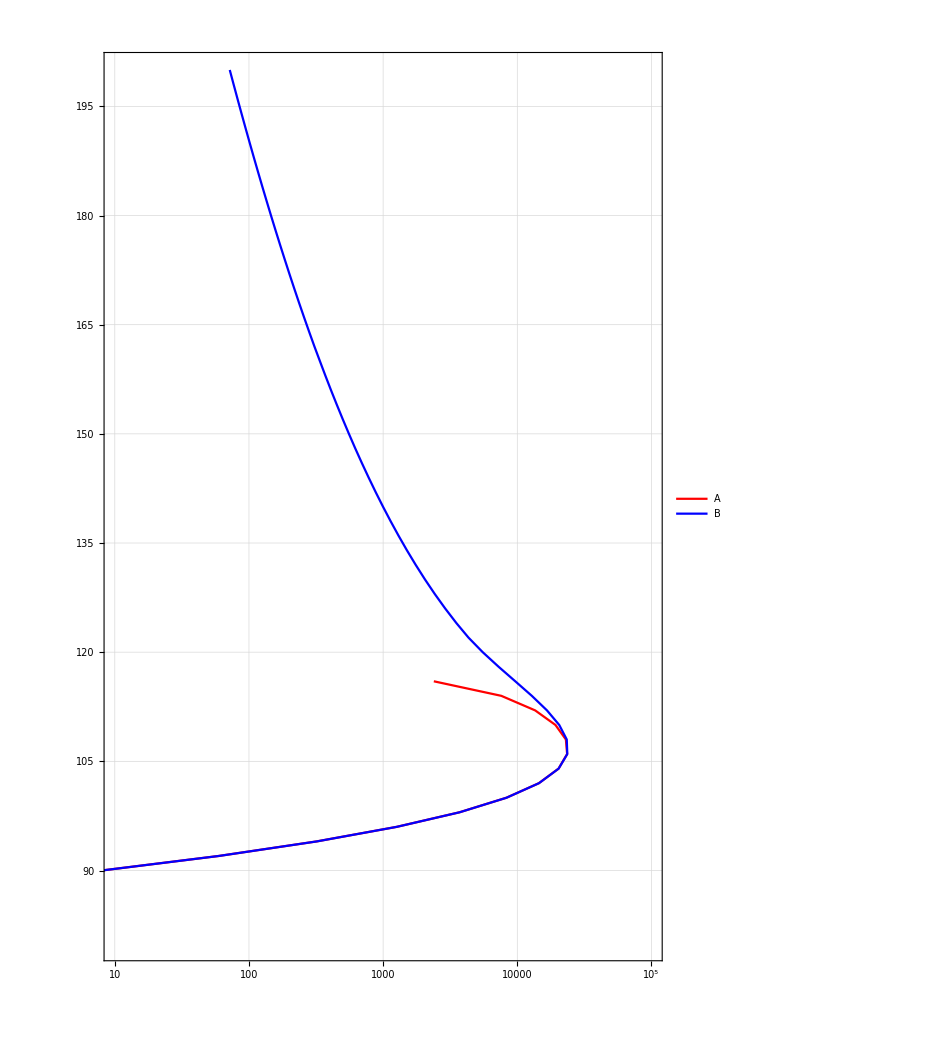

```mathematica
erg2kev=6.24150648 10^8;
Q0keV=1erg2kev;(*keV*)
E0keV=2;(*keV*)
V0keV=5;(*keV*)
deps=35 10^-3;(*keV*)
lbins=63;
EbinA=10^Subdivide[-1,3,lbins];(*keV*)
EbinB=10^Subdivide[Log10[V0keV],3,lbins];
dEbinA=EbinA[[2;;]]-EbinA[[;;-2]];
dEbinB=EbinB[[2;;]]-EbinB[[;;-2]];
EbinA=(EbinA[[2;;]]+EbinA[[;;-2]])/2;(*midpoint rule*)
EbinB=(EbinB[[2;;]]+EbinB[[;;-2]])/2;(*midpoint rule*)
phiA=Q0keV/(2 E0keV^3)(EbinA-V0keV) Exp[(V0keV-EbinA)/E0keV];
phiB=Q0keV/(2 E0keV^3)(EbinB-V0keV) Exp[(V0keV-EbinB)/E0keV];
dQ0A=EbinA phiA dEbinA;
dQ0B=EbinB phiB dEbinB;
ybinA=2/EbinA(#/(6 10^-6))^0.7&/@(ρ H);
ybinB=2/EbinB(#/(6 10^-6))^0.7&/@(ρ H);
fbinA=f[#,EbinA,2010]&/@ybinA;
fbinB=f[#,EbinB,2010]&/@ybinB;
qtot2010A=fbinA.dQ0A/deps/H;
qtot2010B=fbinB.dQ0B/deps/H;
plot=ListLogLinearPlot[{
Transpose[{qtot2010A,z 10^-5}]
,Transpose[{qtot2010B,z 10^-5}]
}
,PlotRange->{{10,10^5},{80,200}}
,AspectRatio->3/2
,Joined->True
(*,PlotMarkers->"OpenMarkers"*)
,PlotStyle->{Red,Blue}
,FrameLabel->{{"",""},{"","V_0 = "<>ToString[V0keV]<>" keV, E_0 = "<>ToString[E0keV]}}
,PlotLegends->{"A","B"}
,Frame->True
,FrameLabel->{"total ionization rate [cm^-3 s^-1]","altitude [km]"}
,GridLines->All
,ImageSize->700
,LabelStyle->Directive[20,Black]
]
```

## Accelerated with LET (Meier 1989)

```mathematica
PHIM[EE_]:=Q0/(2 E0^3)EE Exp[-EE/E0]
PHImax=PHIM[E0];
b=Piecewise[{{(0.8E0)^-1,E0<0.5}},(0.1E0+0.35)^-1];
phi=PHIM[EE]+0.4PHImax E0/EE Exp[-EE b];
f=Table[Integrate[FullSimplify[phi(2E0)/Q0/.E0->EE0],{EE,0.01,∞}],{EE0,{0.1,0.25,0.5,1,2,4,5}}]
```

{1.23421,1.36238,1.46135,1.47842,1.5074,1.55234,1.57053}

```mathematica
phis=Table[phi/.{Q0->1erg2kev,E0->EE0},{EE0,{0.1,0.25,0.5,1,2,4,5}}]/f;
```

```mathematica
erg2kev=6.24150648 10^8;
plot=LogLogPlot[phis,{EE,0.01,100}
,PlotRange->{{0.01,100},{10^(1+3),10^(8+3)}}
,GridLines->Automatic
,AspectRatio->1/GoldenRatio
,ImageSize->800
,PlotStyle->{Red}
,Frame->True
,PlotLegends->Placed[{"Meier 1989"},{Left,Bottom}]
,FrameStyle->Directive[Black,20]
,LabelStyle->Directive[Black,18]
,FrameLabel->{"E [keV]","ϕ [keV^-1 s^-1 cm^-2]"}
]
```

```mathematica
phi/.EE->E0+V0
```

```mathematica
Series[phi,{EE,V0,1}]
Series[LET,{EE,V0,0}]
Series[0.1LET+phi,{EE,V0,0}]
```

```mathematica
phi=Q0/(2 E0^2)((EE-V0)/E0 Exp[-(EE-V0)/E0]);
LET=Q0/(2 E0^2)E0/EE;
erg2kev=6.24150648 10^8;
Manipulate[
LogLogPlot[{
phi/.{Q0->1 erg2kev,E0->EE0,V0->VV0}
,LET/.{Q0->1 erg2kev,E0->EE0,V0->VV0}
},{EE,0.1,1000}
,PlotRange->{{0.1,50},{10^1,10^10}}
,GridLines->{{VV0},All}
,AspectRatio->1/2
,ImageSize->800
,PlotStyle->{Red,{Red,Dashed},Blue}
,Frame->True
,PlotLegends->Placed[{"Maxwellian","LET"},{Left,Bottom}]
,FrameStyle->Directive[Black,20]
,LabelStyle->Directive[Black,18]
,FrameLabel->{"E [keV]","ϕ [keV^-1 s^-1 cm^-2]"}
]
,{EE0,1,10}
,{{VV0,1},0,10}
]
```

## Tests

```mathematica
as={n>0,m>0,E0>0,dv>0,κ>2};
dfv=n/π^(3/2)(m/(2E0))^(3/2)Exp[-(m v^2)/(2 E0)]4π v^2 dv;
dfv=(Q0 m^2)/(16π E0^3) Exp[-(m v^2)/(2 E0)]4π v^2 dv;
dfE=FullSimplify[dfv/.{v->Sqrt[2EE/m],dv->dE/Sqrt[2m EE]},Assumptions->as];
dϕE=FullSimplify[v dfv/.{v->Sqrt[2EE/m],dv->dE/Sqrt[2m EE]},Assumptions->as]
Integrate[dfv/dv,{v,0,∞},Assumptions->as]
Integrate[dfE/dE,{EE,0,∞},Assumptions->as]
2/(3n)Integrate[(m v^2)/2 dfv/dv,{v,0,∞},Assumptions->as]
1/(1/(2n)Integrate[2/(m v^2) dfv/dv,{v,0,∞},Assumptions->as])
```

```mathematica
dfv=n/π^(3/2)(m/(2E0))^(3/2)Gamma[κ+1]/(κ^(3/2)Gamma[κ-1/2])(1+(m v^2)/(κ 2E0))^(-κ-1)4π v^2 dv;
dfE=FullSimplify[dfv/.{v^2->2EE/m,dv->dE/Sqrt[2m EE]},Assumptions->as]
Integrate[dfv/dv,{v,0,∞},Assumptions->as]
Integrate[dfE/dE,{EE,0,∞},Assumptions->as]
2/(3n)Integrate[(m v^2)/2 dfv/dv,{v,0,∞},Assumptions->as]
1/(1/(2n)Integrate[2/(m v^2) dfv/dv,{v,0,∞},Assumptions->as])
```

```mathematica
dϕE=FullSimplify[v dfv/.{v->Sqrt[2EE/m],dv->dE/Sqrt[2m EE]},Assumptions->as]
test=n Sqrt[8/(π m E0^3)] Gamma[κ+1]/(κ^(3/2)Gamma[κ-1/2])EE(1+EE/(κ E0))^(-1-κ)dE;
FullSimplify[dϕE/test,Assumptions->as]
```

```mathematica
phi1=Q0/(2 E0^3)EE Exp[-EE/E0];
phi2=Q0/(2 E0^3)Gamma[κ+1]/(κ^(3/2)Gamma[κ-1/2])EE(1+EE/(κ E0))^(-1-κ);
phi3=Q0/(2 E0^3)((κ-1)(κ-2))/κ^2 EE(1+EE/(κ E0))^(-1-κ);
Integrate[phi1,{EE,0,∞},Assumptions->as]
Integrate[phi2,{EE,0,∞},Assumptions->as]/.E0->E0 κ/(κ-1/2)//FullSimplify
Integrate[phi3,{EE,0,∞},Assumptions->as]/.E0->E0 κ/(κ-1/2)//FullSimplify
```

```mathematica
q=1;
FullSimplify[Integrate[EE^q phi1,{EE,0,∞},Assumptions->as]/Integrate[phi1,{EE,0,∞},Assumptions->as],Assumptions->as]
FullSimplify[Integrate[EE^q phi2,{EE,0,∞},Assumptions->as]/Integrate[phi2,{EE,0,∞},Assumptions->as],Assumptions->as]
FullSimplify[Integrate[EE^q phi3,{EE,0,∞},Assumptions->as]/Integrate[phi3,{EE,0,∞},Assumptions->as],Assumptions->as]
```

```mathematica
Print["(∫_0)^∞/(∫_0)^∞=(∫_0)^∞/(∫_0)^∞=2E_0κ/(κ - 2)"]
Print["(∫_0)^∞/(∫_0)^∞=(∫_0)^∞/(∫_0)^∞=1/E_0(κ - 1)/κ"]
Print["ϕ_κ(E)=Q_0/(2 SuperscriptBox[SubscriptBox[E, 0], 3])(Γ (κ + 1))/κ^(3/2)E(1+E/κE_0)^(-1 - κ)"]
```

```mathematica
LogLogPlot[{
phi1/.{Q0->1,E0->1,κ->5}
,phi2/.{Q0->1,E0->1,κ->5}
,phi3/.{Q0->1,E0->1,κ->5}
},{EE,0.1,1000}]
```

```mathematica
k=Range[64];
lbins=64;
EbinGEMINI=(10.^(-1+4.*(k)/(lbins-1))+10.^(-1+4.*(k-1)/(lbins-1)))/2;
dEbinGEMINI=10.^(-1+4.*(k)/(lbins-1))-10.^(-1+4.*(k-1)/(lbins-1));
Chop[EbinGEMINI[[;;-2]]-EbinA]
Chop[dEbinGEMINI[[;;-2]]-dEbinA]
```

```mathematica
k=Range[64];
lbins=64;
EbinGEMINI=(10.^(Log10[V0keV]+(3-Log10[V0keV])*(k)/(lbins-1))+10.^(Log10[V0keV]+(3-Log10[V0keV])*(k-1)/(lbins-1)))/2;
dEbinGEMINI=10.^(Log10[V0keV]+(3-Log10[V0keV])*(k)/(lbins-1))-10.^(Log10[V0keV]+(3-Log10[V0keV])*(k-1)/(lbins-1));
Chop[EbinGEMINI[[;;-2]]-EbinB]
Chop[dEbinGEMINI[[;;-2]]-dEbinB]
```

```mathematica
lbins=64;
k=Range[lbins];
EbinGEMINI=(10.^(-1+4.*(k)/(lbins-1))+10.^(-1+4.*(k-1)/(lbins-1)))/2
dEbinGEMINI=10.^(-1+4.*(k)/(lbins-1))-10.^(-1+4.*(k-1)/(lbins-1))
```

```mathematica
lbins={1,64,128,256};
tbins={7 60+46.727,12 60+54.866,17 60+44.308,27 60+46.627};
tdata=Transpose[{lbins,tbins/tbins[[1]]}];
tfit=Fit[tdata,{1,x},x]
Show[ListPlot[tdata],Plot[tfit,{x,0,256}]]
```

## Rigorous Drifted Maxwellian

```mathematica
as={E0>0,V0>0,u>0,m>0,n>0,x>0,y>0};
fM=n(m/(π 2E0))^(3/2)Exp[-(vx^2+vy^2+vz^2)/(2E0/m)];(*Regular Maxwellian Velocity Distribution*)
fA=n(m/(π 2E0))^(3/2)Exp[-(vx^2+vy^2+(vz-u)^2)/(2E0/m)];(*Maxwellian Velocity Distribution shifted by u = √(2Subscript[V, 0]/m)*)
Integrate[fM,{vx,-∞,∞},{vy,-∞,∞},{vz,-∞,∞},Assumptions->as](*both normalize to n*)
Integrate[fA,{vx,-∞,∞},{vy,-∞,∞},{vz,-∞,∞},Assumptions->as]
```

every e^- has been shifted in the z direction. accelerated max vs drifted max. in fridman and lemaire paper followed up on knight+

```mathematica
vtoE={v->Sqrt[2EE/m],u->Sqrt[2V0/m],dv->dE/Sqrt[2m EE]};
ddPHIM=FullSimplify[
2π(*integrated over ϕ*)v Cos[θ](*Subscript[v, z]*)n(m/(π 2E0))^(3/2)Exp[-v^2/(2E0/m)](*Maxwellian distribution function in spherical coordinates*)4π v^2(*Jacobian*)dv dθ
/.vtoE,Assumptions->as]
ddPHIA=FullSimplify[2π v Cos[θ]n(m/(π 2E0))^(3/2)Exp[-(v^2+u^2-2u v Cos[θ])/(2E0/m)]4π v^2 dv dθ/.vtoE,Assumptions->as]
```

```mathematica
dPHIM=FullSimplify[Integrate[ddPHIM/dθ,{θ,0,π/2},Assumptions->as],Assumptions->as]
dPHIA=FullSimplify[Integrate[ddPHIA/dθ,{θ,0,π/2},Assumptions->as],Assumptions->as]
dPHIAold=dPHIM/.EE/E0->EE-V0
```

```mathematica
nM=Solve[Q0==Integrate[EE dPHIM/dE,{EE,0,∞},Assumptions->as],n][[1,1,2]];
nA=Solve[Q0==Integrate[EE dPHIA/dE,{EE,0,∞},Assumptions->as],n][[1,1,2]];
nAold=Solve[Q0==Integrate[EE dPHIAold/dE,{EE,V0,∞},Assumptions->as],n][[1,1,2]];
```

```mathematica
dPHIMfull=FullSimplify[dPHIM/.n->nM,Assumptions->as]
dPHIAfull=FullSimplify[dPHIA/.n->nA,Assumptions->as]/.m->1
dPHIAfullold=FullSimplify[dPHIAold/.n->nAold,Assumptions->as]
```

```mathematica
erg2kev=6.24150648 10^8;
LogLogPlot[{
dPHIMfull/dE/.{Q0->1 erg2kev,E0->1}
,dPHIMfull/dE/.{Q0->1 erg2kev,E0->5}
,dPHIAfull/dE/.{Q0->1 erg2kev,E0->1,V0->0.01}
,dPHIAfull/dE/.{Q0->1 erg2kev,E0->1,V0->5}
,dPHIAfullold/dE/.{Q0->1 erg2kev,E0->1,V0->5}
(*,dPHIAfull/.{Q0->1 erg2kev,E0->0.1,V0->5}
,dPHIAfullold/.{Q0->1 erg2kev,E0->0.1,V0->5}*)
},{EE,0.1,100}
,PlotRange->{{0.5,200},{10^1,10^9}}
,GridLines->{{1,3,8},All}
,AspectRatio->1/2
,ImageSize->800
,PlotStyle->{Black,{Black,Dashed},Green,Red,{Red,Dashed},Blue,{Blue,Dashed}}
,Frame->True
,PlotLegends->Placed[{"Max E_0 = 1 keV","Max E_0 = 5 keV","E_0, V_0 = 1, 0.01 keV","E_0, V_0 = 1, 5 keV","old E_0, V_0 = 1, 5 keV","E_0, V_0 = 0.1, 5 keV","E_0, V_0 = 0.1, 5 keV"},{Right,Top}]
,FrameStyle->Directive[Black,20]
,LabelStyle->Directive[Black,18]
,FrameLabel->{"E [keV]","ϕ [keV^-1 s^-1 cm^-2]"}
]
```

```mathematica
dPHIa=FullSimplify[dPHIAfull/.{V0->y E0,EE->x E0,dE->dx E0},Assumptions->as]
dPHIaold=FullSimplify[dPHIAfullold/.{EE->x E0,V0->y E0,dE->dx E0},Assumptions->as]
dPHIaapprox=Normal[Series[dPHIa,{y,0,5}]];
```

```mathematica
ys={10^-15.,0.5,1,5,10,50};
plotting=Table[E0/Q0 dPHIa/dx/.y->yy,{yy,ys}];
legends=Table["V_0/E_0 = "<>ToString[Chop[yy]],{yy,ys}];
plotfull=LogLogPlot[plotting,{x,0.05,500}
,Frame->True
,FrameLabel->{"x = E/E_0","dΦ_a(x)/dx [Q_0/E_0]"}
,FrameStyle->Directive[Black,20]
,LabelStyle->Directive[Black,20]
,PlotRange->{{0.05,500},{10^-10,1}}
,PlotStyle->Table[RGBColor[r,0,0],{r,0,1,0.2}]
,PlotLegends->Placed[legends,{Right,Top}]
,ImageSize->800
,GridLines->Automatic
]
```

```mathematica
ys={10^-15.,0.5,1,5,10,50};
plotting=Table[E0/Q0 dPHIaold/dx/.y->yy,{yy,ys}];
legends=Table["V_0/E_0 = "<>ToString[Chop[yy]],{yy,ys}];
plotold=LogLogPlot[plotting,{x,0.05,500}
,Frame->True
,FrameLabel->{"x = E/E_0","dΦ_a(x)/dx [Q_0/E_0]"}
,FrameStyle->Directive[Black,20]
,LabelStyle->Directive[Black,20]
,PlotRange->{{0.05,500},{10^-10,1}}
,PlotStyle->Table[{RGBColor[r,0,0],Dashed},{r,0,1,0.2}]
,PlotLegends->Placed[legends,{Right,Top}]
,ImageSize->800
,GridLines->Automatic
]
```

```mathematica
Show[plotfull,plotold]
```

## Fridman and Lemaire 1980

```mathematica
as={Ne>0,me>0,E0pe>0,E0pa>0,eV>0,x>0,b>1};
v2E={vpe->Sqrt[2Epe/me],dvpe->dEpe/Sqrt[2me Epe],vpa->Sqrt[2Epa/me],dvpa->dEpa/Sqrt[2me Epa]};
fvdv=Ne(me/(2π))^(3/2)1/(E0pa^(1/2)E0pe)Exp[-(1/2 me vpe^2)/E0pe-(1/2 me vpa^2)/E0pa]vpe dvpe dvpa dϕ;
fEdE=FullSimplify[fvdv/.v2E,Assumptions->as];
```

```mathematica
Print["(f (v) SuperscriptBox[d, 3] v)/(dv_(||)) = ",fvdv/(dvpe dvpa dϕ)]
Print["(f (E) SuperscriptBox[d, 3] E)/(dE_(||)) = ",fEdE/(dEpe dEpa dϕ)]
```

```mathematica
dJpa=Integrate[Sqrt[(2Epa)/me] dfE/(dEpe dϕ),{Epe,0,E0pe/E0pa x(Epa+eV)},{ϕ,0,2π},Assumptions->as]
dϵ=Integrate[Sqrt[(2Epa)/me]Epa dfE/(dEpe dϕ),{Epe,0,E0pe/E0pa x(Epa+eV)},{ϕ,0,2π},Assumptions->as]
```

```mathematica
Jpa=FullSimplify[Integrate[dJpa/dEpa,{Epa,0,∞},Assumptions->as],Assumptions->as];
ϵ=FullSimplify[Integrate[dϵ/dEpa,{Epa,0,∞},Assumptions->as],Assumptions->as];
Jpa2=Ne Sqrt[E0pa/(2π me)](1-Exp[-eV x/E0pa]/(1+x));
ϵ2=Ne Sqrt[E0pa/(2π me)]E0pa(1-Exp[-eV x/E0pa]/(1+x)^2);
FullSimplify[Jpa/Jpa2,Assumptions->as]
FullSimplify[ϵ/ϵ2,Assumptions->as]
```

```mathematica
Solve[EpaI==EpaS-EpeS(b-1)+eV,EpeS][[1,1,2]]
```

```mathematica
Integrate[fEdE/(dϕ dEpe)/.Epe->0,{ϕ,0,2π}]
```

```mathematica
FullSimplify[vpa fvdv/.v2E,Assumptions->as]
```

```mathematica
EE/E0 Exp[-EE/E0]
```